```mathematica
tocka[i_,n_]:=With[{φ=2π i/n},{Cos[φ],Sin[φ]}]
```

```mathematica
naloga3a[n_,sez_]:=
Graphics[{
Table[
Point[tocka[i,n]],
{i,0,n-1}
],
Table[
Line[{tocka[i,n],tocka[i+k,n]}],
{i,0,n-1},{k,sez}
]
}]
```

```mathematica
naloga3b[n_]:=naloga3a[n,Select[Range[1,n/2],CoprimeQ[n,#]&]]
```

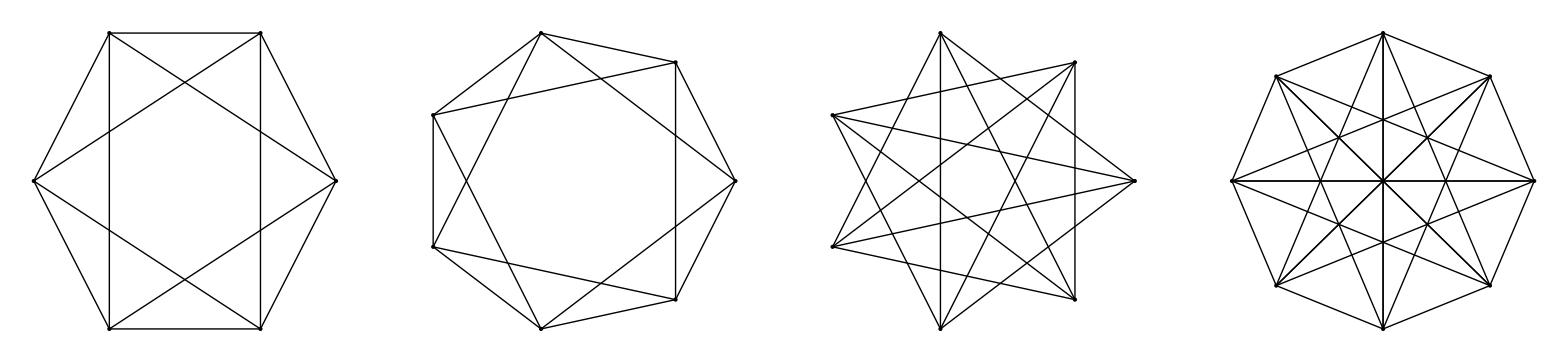

```mathematica
GraphicsRow[{naloga3a[6,{1,2}],naloga3a[7,{1,2}],naloga3a[7,{3,5}],naloga3a[8,{1,3,4}]}]
```

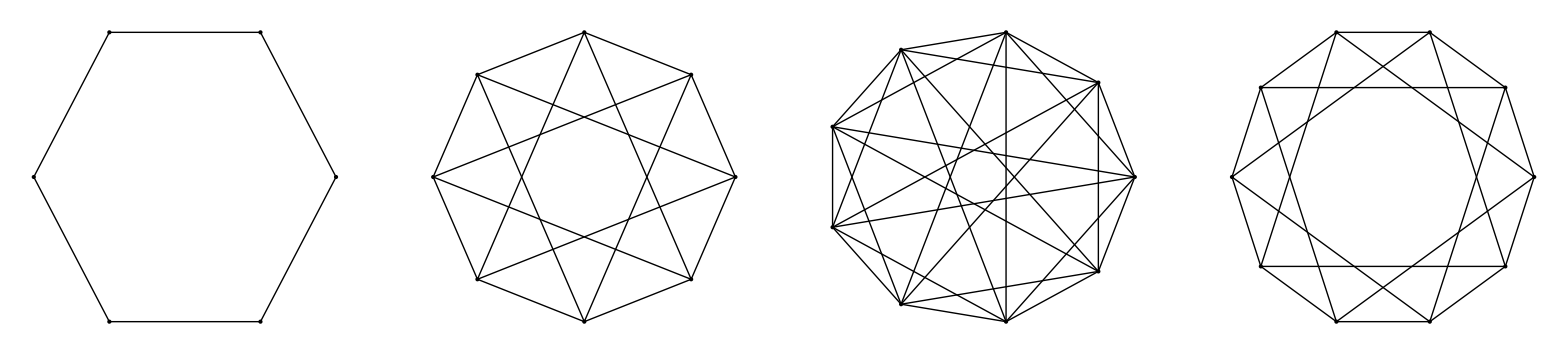

```mathematica
GraphicsRow[{naloga3b[6],naloga3b[8],naloga3b[9],naloga3b[10]}]
```

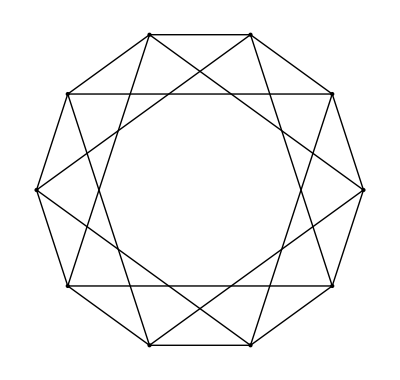

```mathematica
naloga3[10,{1,3}]
```